```mathematica
PacletDirectoryLoad[]
Needs["Wolfram`TensorNetworks`"]
```

{/Users/mohammadb/Documents/GitHub/TensorNetworks/}

## Playground

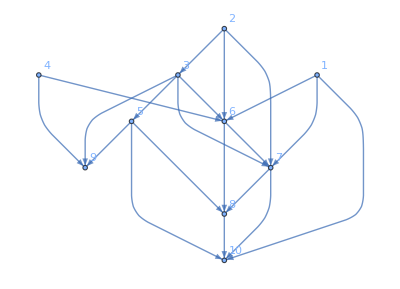

```mathematica
net=ToTensorNetworkGraph[RandomGraph[{10,20}],Method->"RandomComplex"]
```

```mathematica
TensorNetworkContract[net]//AbsoluteTiming
```

{0.00515,-13.8364-46.3534 ⅈ}

```mathematica
TensorNetworkContract[net,Method->"Naive"]//AbsoluteTiming
```

{0.00583,-13.8364-46.3534 ⅈ}

```mathematica
path=TensorNetworkFindContractionPath[net,Method->"max"]
```

{{6,10},{7,9},{7,8},{6,7},{3,6},{4,5},{2,4},{2,3},{1,2}}

```mathematica
Activate/@AssociationMap[TensorNetworkContraction[net,path,Method->#]&,$TensorNetworkContractionMethods]
```

<|ArrayDotTranspose→-13.8364-46.3534 ⅈ,ArrayDot→-13.8364-46.3534 ⅈ,Dot→-13.8364-46.3534 ⅈ,TensorContract→-13.8364-46.3534 ⅈ,TableSum→-13.8364-46.3534 ⅈ|>

```mathematica
tn=TensorNetwork[{{1,2},{1,3},{1,4}}]
```

TensorNetwork[…]

Missing[UnknownProperty,ToBinary]

```mathematica
TensorNetworkContract[tn]
```

TensorContract[T2dd⊗T2dd⊗T2dd⊗d,d,d1,2,3,{{1,7},{3,8},{5,9}}]